```mathematica
(*Bader analysis- ZrC with and without interstitial Frenkel defect*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/DOS_Bader_defect/DOS_Bader_out_4685"];
baderFile={"comparison_bader","comparison_bader_Zr","comparison_bader_C"};
bader=Table[ReadList[baderFile[[i]],Table[Number,{i,15}]],{i,1,3}];
```

```mathematica
header={"#"," X", "Y" ,"Z" ,"CHARGE" ,"MIN DIST", "ATOMIC VOL", "#" ,"X" ,"Y" ,"Z", "CHARGE" "min DIST" ,"ATOMIC VOL"};
```

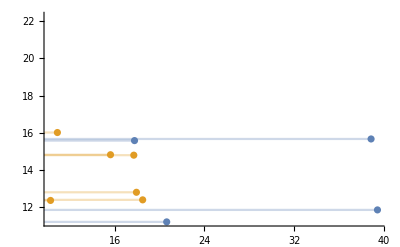

```mathematica
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[{RandomReal[{10,50},{6,2}],RandomReal[{10,20},{6,2}]}]
```

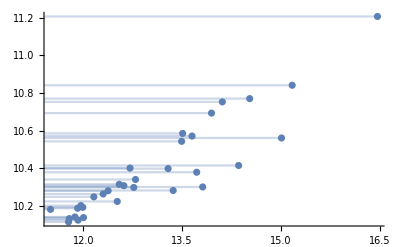

```mathematica
horizontalListPlotFill[ListPlot[zrDefect]]
```

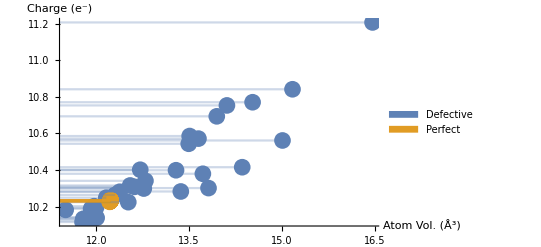

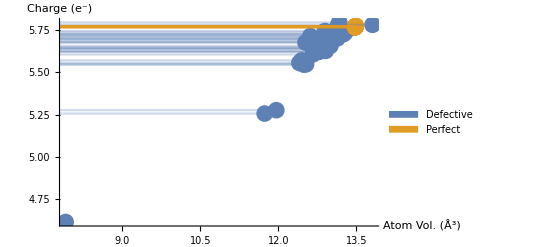

```mathematica
zrDefect=Transpose@{Transpose[bader[[2]]][[7]],Transpose[bader[[2]]][[5]]};
zrPerfect=Transpose@{Transpose[bader[[2]]][[14]],Transpose[bader[[2]]][[12]]};

cDefect=Transpose@{Transpose[bader[[3]]][[7]],Transpose[bader[[3]]][[5]]};
cPerfect=Transpose@{Transpose[bader[[3]]][[14]],Transpose[bader[[3]]][[12]]};

plot1=horizontalListPlotFill@ListPlot[{zrDefect,zrPerfect},PlotRange->All,ImageSize->400,PlotStyle->PointSize[0.03],AxesLabel->{"Atom Vol. (Å^3)","Charge (e^-)"},PlotLegends->SwatchLegend[{"Defective","Perfect"}]]
plot2=horizontalListPlotFill@ListPlot[{cDefect,cPerfect},PlotRange->All,ImageSize->400,PlotStyle->PointSize[0.03],AxesLabel->{"Atom Vol. (Å^3)","Charge (e^-)"},PlotLegends->SwatchLegend[{"Defective","Perfect"}]]
GraphicsGrid[{{plot1,plot2}}];
```

```mathematica
(*Frenkel defect oxidises Carbon. Most, the Lowest atom 57 - intersititial C, next 41 and 53, the others in the C-C-C unit*)
(*Frenkel defect reduces carbon. Most, the Lowest atom 57 - intersititial C, next 41 and 53, the others in the C-C-C unit*)
```